# Non-local QFT: field redefinition

```mathematica
$Assumptions=And[g∈Reals,g≠0,ϕ[t]≠0];
```

```mathematica
path=NotebookDirectory[];
```

## d = 1

### Convergence of coefficients

```mathematica
(*Vpot=VrScaledCan[p];*)
```

```mathematica
p=11;
Vpot=(m^2 ϕ^2)/2+(-1/3-a^2 m^2) ϕ^3+(a^2+(23 a^4 m^2)/6+(112 a^6 m^4)/9+(400 a^8 m^6)/9+(5056 a^10 m^8)/45+(30848 a^12 m^10)/135+(372224 a^14 m^12)/945+(111872 a^16 m^14)/189+(959488 a^18 m^16)/1215+(40306688 a^20 m^18)/42525+(483713024 a^22 m^20)/467775) ϕ^4+(-(13 a^4)/3-(370 a^6 m^2)/9-(2356 a^8 m^4)/9) ϕ^5+((97 a^6)/3+(7444 a^8 m^2)/15+(40016 a^10 m^4)/27+(16951588 a^12 m^6)/2025+(365040328 a^14 m^8)/4725+(704360354 a^16 m^10)/1575+(53044107164 a^18 m^12)/25515+(5345363837636 a^20 m^14)/637875+(212689374482008 a^22 m^16)/7016625) ϕ^6+(-(13532 a^8)/45-(1645424 a^10 m^2)/405-(246594764 a^12 m^4)/6075-(18403444376 a^14 m^6)/42525) ϕ^7+((1057238 a^10)/405+(528895198 a^12 m^2)/8505+(293278365536 a^14 m^4)/297675+(330220197478 a^16 m^6)/297675+(4539699316064 a^18 m^8)/535815+(3762791962092662 a^20 m^10)/13395375+(18508000088422676 a^22 m^12)/5893965) ϕ^8+(-(17612426 a^12)/567-(1376189404 a^14 m^2)/1323-(1461162201244 a^16 m^4)/178605-(152243548796524 a^18 m^6)/1607445-(14516307774038468 a^20 m^8)/8037225) ϕ^9+((17745598574 a^14)/42525+(91967935202338 a^16 m^2)/8037225+(3255947000654108 a^18 m^4)/14467005+(339406560100146388 a^20 m^6)/72335025-(36650456262120146896 a^22 m^8)/3978426375) ϕ^10+(-(5599006958392 a^16)/1148175-(2226671149812904 a^18 m^2)/10333575-(461350316377218328 a^20 m^4)/72335025-(13262953310597307088 a^22 m^6)/795685275) ϕ^11+((604370472837748 a^18)/8037225+(3570960644823919238 a^20 m^2)/795685275+(107753866659559323248 a^22 m^4)/1705039875) ϕ^12+(-(1954323884798776 a^20)/1515591-(60074374172932678156 a^22 m^2)/1023023925) ϕ^13+(11898606015180066008 a^22 ϕ^14)/651015225/.{a->α,m->1};
```

#### In ξ^2

```mathematica
ξ2Table=Table[i,{i,2,2p,2}]
```

{2,4,6,8,10,12,14,16,18,20,22}

α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45+(30848 α^12)/135+(372224 α^14)/945+(111872 α^16)/189+(959488 α^18)/1215+(40306688 α^20)/42525+(483713024 α^22)/467775

{1,23/6,112/9,400/9,5056/45,30848/135,372224/945,111872/189,959488/1215,40306688/42525,483713024/467775}

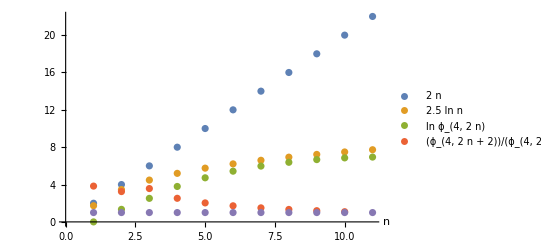

```mathematica
Vϕ4=Coefficient[Vpot,ϕ^4]
Vϕ4Coeff=CoefficientList[Vϕ4,α^2][[2;;p+1]]
Vϕ4CoeffRatio=Table[Vϕ4Coeff[[i+1]]/Vϕ4Coeff[[i]],{i,1,p-1}];
DiscretePlot[{ξ2Table[[i]],2.5Log[ξ2Table[[i]]],Log[Vϕ4Coeff][[i]],Vϕ4CoeffRatio[[i]],1},{i,1,p},
Filling->None,PlotLegends->Placed[{"2 n","2.5 ln n","ln ϕ_(4, 2  n)","(ϕ_(4, 2  n + 2))/(ϕ_(4, 2  n))"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi4_xi2.pdf",%];
```

(97 α^6)/3+(7444 α^8)/15+(40016 α^10)/27+(16951588 α^12)/2025+(365040328 α^14)/4725+(704360354 α^16)/1575+(53044107164 α^18)/25515+(5345363837636 α^20)/637875+(212689374482008 α^22)/7016625

{97/3,7444/15,40016/27,16951588/2025,365040328/4725,704360354/1575,53044107164/25515,5345363837636/637875,212689374482008/7016625}

{7444/485,50020/16749,4237897/750300,273780246/29665279,1056540531/182520164,132610267910/28526594337,1336340959409/331525669775,53172343620502/14699750553499}

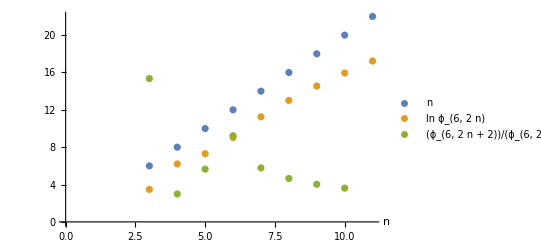

```mathematica
Vϕ6=Coefficient[Vpot,ϕ^6]
Vϕ6Coeff=CoefficientList[Vϕ6,α^2][[4;;p+1]]
Vϕ6CoeffRatio=Table[Vϕ6Coeff[[i+1]]/Vϕ6Coeff[[i]],{i,1,p-3}]
DiscretePlot[{ξ2Table[[i]],Log[Vϕ6Coeff][[i-2]],Vϕ6CoeffRatio[[i-2]]},{i,3,p},Filling->None,PlotLegends->Placed[{"n","ln ϕ_(6, 2  n)","(ϕ_(6, 2  n + 2))/(ϕ_(6, 2  n))"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi6_xi2.pdf",%];
```

(1057238 α^10)/405+(528895198 α^12)/8505+(293278365536 α^14)/297675+(330220197478 α^16)/297675+(4539699316064 α^18)/535815+(3762791962092662 α^20)/13395375+(18508000088422676 α^22)/5893965

{0,1057238/405,528895198/8505,293278365536/297675,330220197478/297675,4539699316064/535815,3762791962092662/13395375,18508000088422676/5893965}

{1057238/13095,264447599/2110374,18329897846/27573525,165110098739/1245941718,2837312072540/25872233247,1881395981046331/2995292405385,4627000022105669/3063297188721}

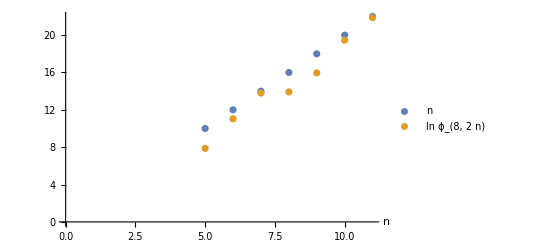

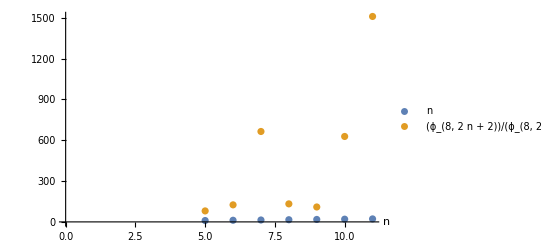

```mathematica
Vϕ8=Coefficient[Vpot,ϕ^8]
Vϕ8Coeff=CoefficientList[Vϕ8,α^2][[5;;p+1]]
Vϕ8CoeffRatio=Table[Vϕ8Coeff[[i+1]]/Vϕ6Coeff[[i]],{i,1,p-4}]
DiscretePlot[{ξ2Table[[i]],Log[Vϕ8Coeff][[i-3]]},{i,5,p},Filling->None,PlotLegends->Placed[{"n","ln ϕ_(8, 2  n)"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi8_xi2_log.pdf",%];
DiscretePlot[{ξ2Table[[i]],Vϕ8CoeffRatio[[i-4]]},{i,5,p},Filling->None,PlotLegends->Placed[{"n","(ϕ_(8, 2  n + 2))/(ϕ_(8, 2  n))"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}]
Export[path<>"coeff_phi8_xi2_ratio.pdf",%];
```

#### In ϕ

```mathematica
VϕCoeff=CoefficientList[Vpot,ϕ][[3;;]]
VϕCoeffRatio=Table[VϕCoeff[[i+1]]/VϕCoeff[[i]],{i,1,12}]//Simplify
```

{1/2,-1/3-α^2,α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45+(30848 α^12)/135+(372224 α^14)/945+(111872 α^16)/189+(959488 α^18)/1215+(40306688 α^20)/42525+(483713024 α^22)/467775,-(13 α^4)/3-(370 α^6)/9-(2356 α^8)/9,(97 α^6)/3+(7444 α^8)/15+(40016 α^10)/27+(16951588 α^12)/2025+(365040328 α^14)/4725+(704360354 α^16)/1575+(53044107164 α^18)/25515+(5345363837636 α^20)/637875+(212689374482008 α^22)/7016625,-(13532 α^8)/45-(1645424 α^10)/405-(246594764 α^12)/6075-(18403444376 α^14)/42525,(1057238 α^10)/405+(528895198 α^12)/8505+(293278365536 α^14)/297675+(330220197478 α^16)/297675+(4539699316064 α^18)/535815+(3762791962092662 α^20)/13395375+(18508000088422676 α^22)/5893965,-(17612426 α^12)/567-(1376189404 α^14)/1323-(1461162201244 α^16)/178605-(152243548796524 α^18)/1607445-(14516307774038468 α^20)/8037225,(17745598574 α^14)/42525+(91967935202338 α^16)/8037225+(3255947000654108 α^18)/14467005+(339406560100146388 α^20)/72335025-(36650456262120146896 α^22)/3978426375,-(5599006958392 α^16)/1148175-(2226671149812904 α^18)/10333575-(461350316377218328 α^20)/72335025-(13262953310597307088 α^22)/795685275,(604370472837748 α^18)/8037225+(3570960644823919238 α^20)/795685275+(107753866659559323248 α^22)/1705039875,-(1954323884798776 α^20)/1515591-(60074374172932678156 α^22)/1023023925,(11898606015180066008 α^22)/651015225}

{-2/3-2 α^2,-(3 (α^2+(23 α^4)/6+(112 α^6)/9+(400 α^8)/9+(5056 α^10)/45+(30848 α^12)/135+(372224 α^14)/945+(111872 α^16)/189+(959488 α^18)/1215+(40306688 α^20)/42525+(483713024 α^22)/467775))/(1+3 α^2),-(103950 α^2 (39+370 α^2+2356 α^4))/(935550+3586275 α^2+11642400 α^4+41580000 α^6+105114240 α^8+213776640 α^10+368501760 α^12+553766400 α^14+738805760 α^16+886747136 α^18+967426048 α^20),-(α^2 (226870875+3482117100 α^2+10399158000 α^4+58737252420 α^6+542084887080 α^8+3137925377070 α^10+14587129470100 α^12+58799002213996 α^14+212689374482008 α^16))/(779625 (39+370 α^2+2356 α^4)),-(660 α^2 (3196935+43192380 α^2+431540837 α^4+4600861094 α^6))/(226870875+3482117100 α^2+10399158000 α^4+58737252420 α^6+542084887080 α^8+3137925377070 α^10+14587129470100 α^12+58799002213996 α^14+212689374482008 α^16),-(α^2 (192324807675+4581554652675 α^2+72586395470160 α^4+81729498875805 α^6+624208655958800 α^8+20695355791509641 α^10+231350001105283450 α^12))/(6930 (3196935+43192380 α^2+431540837 α^4+4600861094 α^6)),-(55 α^2 (124828069275+4180175314650 α^2+32876149527990 α^4+380608871991310 α^6+7258153887019234 α^8))/(3 (192324807675+4581554652675 α^2+72586395470160 α^4+81729498875805 α^6+624208655958800 α^8+20695355791509641 α^10+231350001105283450 α^12)),(α^2 (-830094737295285-22762063962578655 α^2-447692712589939850 α^4-9333680402754025670 α^6+18325228131060073448 α^8))/(495 (124828069275+4180175314650 α^2+32876149527990 α^4+380608871991310 α^6+7258153887019234 α^8)),(20 α^2 (485013977770707+21431709816949201 α^2+634356685018675201 α^4+1657869163824663386 α^6))/(-830094737295285-22762063962578655 α^2-447692712589939850 α^4-9333680402754025670 α^6+18325228131060073448 α^8),-(α^2 (448745076082027890+26782204836179394285 α^2+377138533308457631368 α^4))/(60 (485013977770707+21431709816949201 α^2+634356685018675201 α^4+1657869163824663386 α^6)),-(70 α^2 (329792155559793450+15018593543233169539 α^2))/(3 (448745076082027890+26782204836179394285 α^2+377138533308457631368 α^4)),-(32721166541745181522 α^2)/(2308545088918554150+105130154802632186773 α^2)}

```mathematica
plotVCoeff[αp_]:=Module[{g1,g2},
g1=DiscretePlot[{i,Abs[VϕCoeffRatio[[i-2]]]/.α->αp},{i,3,15},Filling->None,PlotLegends->Placed[{"n","|(ϕ_(n + 1))/ϕ_n|"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}];
Export[path<>"coeff_phi_ratio_xi="<>ToString[αp]<>".pdf",Show[g1,PlotRange->Full]];
g2=DiscretePlot[{i,Log[Abs[VϕCoeff[[i-2]]]]/.α->αp},{i,3,14},Filling->None,PlotLegends->Placed[{"n","ln |ϕ_n|"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}];
Export[path<>"coeff_phi_log_xi="<>ToString[αp]<>".pdf",g2];
GraphicsRow[{Show[g1,PlotRange->Full],Show[g2,PlotRange->Full]}]
];
plotVCoeff[0.3]
plotVCoeff[0.5]
plotVCoeff[0.6]
plotVCoeff[1.1]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
DiscretePlot[{i,Abs[VϕCoeffRatio[[i-2]]]/.α->0.3},{i,3,15},Filling->None,PlotLegends->Placed[{"n","|(ϕ_(n + 1))/ϕ_n|"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}];
DiscretePlot[{i,Log[Abs[VϕCoeff[[i-2]]]]/.α->0.3},{i,3,14},Filling->None,PlotLegends->Placed[{"n","ln |ϕ_n|"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}];
```

```mathematica
Manipulate[
Show[Plot[1,{x,0,14}],
DiscretePlot[{i,Log[Abs[VϕCoeff[[i-2]]]]/.α->αp},{i,3,14},Filling->None,PlotLegends->Placed[{"ϕ^n","ln ϕ_n"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}],PlotRange->Full,ImageSize->Large],
{αp,0.01,1,0.05}]
```

```mathematica
Manipulate[
Show[Plot[1,{x,0,14}],
DiscretePlot[{i,Abs[VϕCoeffRatio[[i-2]]]/.α->αp},{i,3,14},Filling->None,PlotLegends->Placed[{"ϕ^n","(ϕ_(n + 1))/ϕ_n"},Right],AxesLabel->{"n",None},AxesOrigin->{0,0}],PlotRange->Full,ImageSize->Large],
{αp,0.01,1,0.05}]
```

### Study of total derivatives

```mathematica
redefPart=(ϕ[t]^2-m^2 ϕ[t]) δϕ[0][t]-δϕ[0][t] ϕ''[t];
```

```mathematica
D[((Derivative[1][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
%%[[2]];
```

-3/2 m^4 ϕ[t]^3+5/2 m^2 ϕ[t]^4-ϕ[t]^5

```mathematica
D[((Derivative[1][ϕ][t])^5), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

-15/8 m^6 ϕ[t]^5+35/8 m^4 ϕ[t]^6-10/3 m^2 ϕ[t]^7+(5 ϕ[t]^8)/6

```mathematica
D[((Derivative[1][ϕ][t])^7), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

-35/16 m^8 ϕ[t]^7+105/16 m^6 ϕ[t]^8-175/24 m^4 ϕ[t]^9+385/108 m^2 ϕ[t]^10-(35 ϕ[t]^11)/54

```mathematica
D[((Derivative[3][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

-3 m^10 ϕ[t]^3+5 m^8 ϕ[t]^4-2 m^6 ϕ[t]^5

```mathematica
D[(Derivative[1][ϕ][t]Derivative[2][ϕ][t]), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[((Derivative[1][ϕ][t])^3 Derivative[2][ϕ][t]), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[((Derivative[1][ϕ][t])^3(Derivative[2][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[((Derivative[1][ϕ][t])^2 Derivative[2][ϕ][t]Derivative[3][ϕ][t]), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0

```mathematica
D[(Derivative[1][ϕ][t](Derivative[3][ϕ][t])^2), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

3/2 m^8 ϕ[t]^3-5/2 m^6 ϕ[t]^4+m^4 ϕ[t]^5

```mathematica
D[((Derivative[1][ϕ][t])^3(Derivative[3][ϕ][t])^2), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

15/8 m^10 ϕ[t]^5-35/8 m^8 ϕ[t]^6+10/3 m^6 ϕ[t]^7-5/6 m^4 ϕ[t]^8

```mathematica
D[((Derivative[1][ϕ][t])^3(Derivative[3][ϕ][t])^4), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

105/16 m^16 ϕ[t]^7-315/16 m^14 ϕ[t]^8+175/8 m^12 ϕ[t]^9-385/36 m^10 ϕ[t]^10+35/18 m^8 ϕ[t]^11

```mathematica
D[((Derivative[1][ϕ][t])^5(Derivative[3][ϕ][t])^2), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

35/16 m^12 ϕ[t]^7-105/16 m^10 ϕ[t]^8+175/24 m^8 ϕ[t]^9-385/108 m^6 ϕ[t]^10+35/54 m^4 ϕ[t]^11

```mathematica
D[((D[(ϕ[t]^2-m^2 ϕ[t]), t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

3/2 m^10 ϕ[t]^3-5/2 m^8 ϕ[t]^4+m^6 ϕ[t]^5

```mathematica
D[((D[(ϕ[t]^2-m^2 ϕ[t]), t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

3/2 m^10 ϕ[t]^3-5/2 m^8 ϕ[t]^4+m^6 ϕ[t]^5

```mathematica
D[(ϕ[t]^n(Derivative[1][ϕ][t])^3), t]+redefPart;
reduceRecusively[1,%]//Simplify//Expand;
%[[1]]
```

0